```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\shiyi\work\git\work\critical_region\nu_plot

```mathematica
Taylormub0=Import["Taylornumub0.dat"];
Taylormub50=Import["Taylornumub50.dat"];
Taylormub100=Import["Taylornumub100.dat"];
Taylormub150=Import["Taylornumub150.dat"];
Taylormub200=Import["Taylornumub200.dat"];
Taylormub250=Import["Taylornumub250.dat"];
Taylormub300=Import["Taylornumub300.dat"];
Taylormub350=Import["Taylornumub350.dat"];
Taylormub400=Import["Taylornumub400.dat"];
Taylormub450=Import["Taylornumub450.dat"];
Taylormub500=Import["Taylornumub500.dat"];
Taylormub550=Import["Taylornumub550.dat"];
Taylormub600=Import["Taylornumub600.dat"];
Taylormub650=Import["Taylornumub650.dat"];
Taylormub700=Import["Taylornumub700.dat"];
Chebymub0=Import["numub0.dat"];
Chebymub600=Import["numub600.dat"];
Chebymub650=Import["numub650.dat"];
Chebymub700=Import["numub700.dat"];
ChebyTCP=Import["nuTCP.dat"];
```

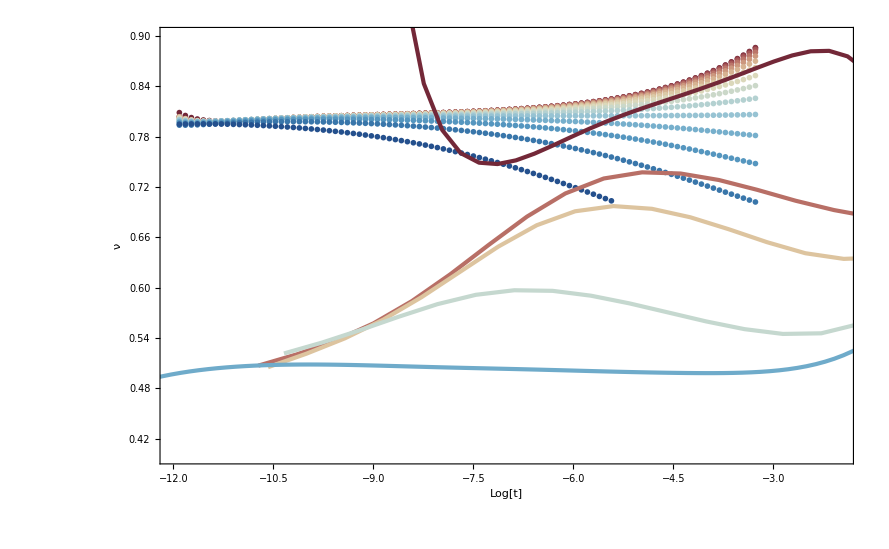

```mathematica
Show[ListPlot[{Taylormub0,Taylormub50,Taylormub100,Taylormub150,Taylormub200,Taylormub250,Taylormub300,Taylormub350,Taylormub400,Taylormub450,Taylormub500,Taylormub550,Taylormub600,Taylormub650,Taylormub700},
Frame->True,FrameLabel->{Style["Log[t]",25,FontFamily->"Times",Black],Style["ν",25,FontFamily->"Times",Black]},
PlotStyle->Table[Directive[ColorData["RedBlueTones"][i],AbsoluteThickness[3.]],{i,0,1,0.0714}],PlotStyle->10,
PlotLegends->Placed[LineLegend[{"μ_B=0","μ_B=50 MeV","μ_B=100 MeV","μ_B=150 MeV","μ_B=200 MeV","μ_B=250 MeV","μ_B=300 MeV","μ_B=350 MeV","μ_B=400 MeV","μ_B=450 MeV","μ_B=500 MeV","μ_B=550 MeV","μ_B=600 MeV","μ_B=650 MeV","μ_B=700 MeV"},LabelStyle->16],{0.23,0.32}],
PlotRange->{{-12,-2},{0.4,0.9}},AxesOrigin->{-12,0.3},FrameTicksStyle->Directive[15,Black]],ListLinePlot[{Transpose[{Log[Transpose[Chebymub0][[1]]],Transpose[Chebymub0][[2]]}],Transpose[{Log[Transpose[Chebymub600][[1]]],Transpose[Chebymub600][[2]]}],Transpose[{Log[Transpose[Chebymub650][[1]]],Transpose[Chebymub650][[2]]}],Transpose[{Log[Transpose[Chebymub700][[1]]],Transpose[Chebymub700][[2]]}],Transpose[{Log[Transpose[ChebyTCP][[1]]],Transpose[ChebyTCP][[2]]}]},
Frame->True,FrameLabel->{Style["Log[t]",25,FontFamily->"Times",Black],Style["ν",25,FontFamily->"Times",Black]},
PlotStyle->Table[Directive[ColorData["RedBlueTones"][i],AbsoluteThickness[3.]],{i,0,1,0.2}],PlotStyle->10,
PlotLegends->Placed[LineLegend[{"μ_B=0","μ_B=600 MeV","μ_B=650 MeV","μ_B=700 MeV","TCP"},LabelStyle->16],{0.23,0.32}]]]
```